```mathematica
ContinuedFraction[Pi, 40]
```

{3,7,15,1,292,1,1,1,2,1,3,1,14,2,1,1,2,2,2,2,1,84,2,1,1,15,3,13,1,4,2,6,6,99,1,2,2,6,3,5}

```mathematica
ContinuedFraction[E, 40]
```

{2,1,2,1,1,4,1,1,6,1,1,8,1,1,10,1,1,12,1,1,14,1,1,16,1,1,18,1,1,20,1,1,22,1,1,24,1,1,26,1}

```mathematica
ContinuedFraction[Sqrt[2], 40]
```

{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
ContinuedFraction[Sqrt[7], 40]
```

{2,1,1,1,4,1,1,1,4,1,1,1,4,1,1,1,4,1,1,1,4,1,1,1,4,1,1,1,4,1,1,1,4,1,1,1,4,1,1,1}

```mathematica
ContinuedFraction[Sqrt[19], 40]
```

{4,2,1,3,1,2,8,2,1,3,1,2,8,2,1,3,1,2,8,2,1,3,1,2,8,2,1,3,1,2,8,2,1,3,1,2,8,2,1,3}

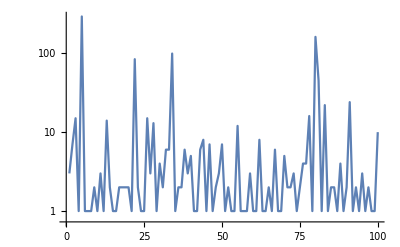

```mathematica
ListLinePlot[ContinuedFraction[Pi, 100], PlotRange->All, ScalingFunctions->"Log"]
```

```mathematica
Manipulate[ListLinePlot[ContinuedFraction[Sqrt[Prime[n]], 50], PlotRange->All, ScalingFunctions->"Log"] , {n, 1, 100, 1}]
```

```mathematica
drift = Table[Total[ContinuedFraction[Pi, x]], {x, 100}]
```

{3,10,25,26,318,319,320,321,323,324,327,328,342,344,345,346,348,350,352,354,355,439,441,442,443,458,461,474,475,479,481,487,493,592,593,595,597,603,606,611,612,613,619,627,628,635,636,638,641,648,649,651,652,653,665,666,667,668,671,672,673,681,682,683,685,686,692,693,694,699,701,703,706,707,709,713,717,733,734,895,940,941,963,964,966,968,969,973,974,976,1000,1001,1003,1004,1007,1008,1010,1011,1012,1022}

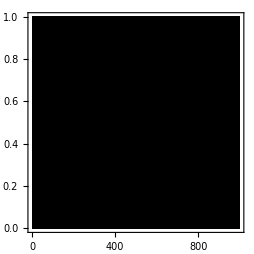

```mathematica
DensityPlot[Abs[Subtract[x, First@Nearest[drift, x]]], {x, 0, 1000}, {y, 0,1}, MaxRecursion->2, PlotTheme->"Monochrome"]
```

```mathematica
drift2 = GetDrift[Sqrt[7], 20]
```

{2,3,4,5,9,10,11,12,16,17,18,19,23,24,25,26,30,31,32,33}

```mathematica
MakeWaves[x_, n_] := Module[{
drift = GetDrift[x, n]
},
DensityPlot[
Abs[Subtract[
t,
First@Nearest[drift, t]]
],
{t, 0, Max[drift]},
{y, 0,1},
 MaxRecursion->4, PlotTheme->"Monochrome", AxesLabel->None
]
]
```

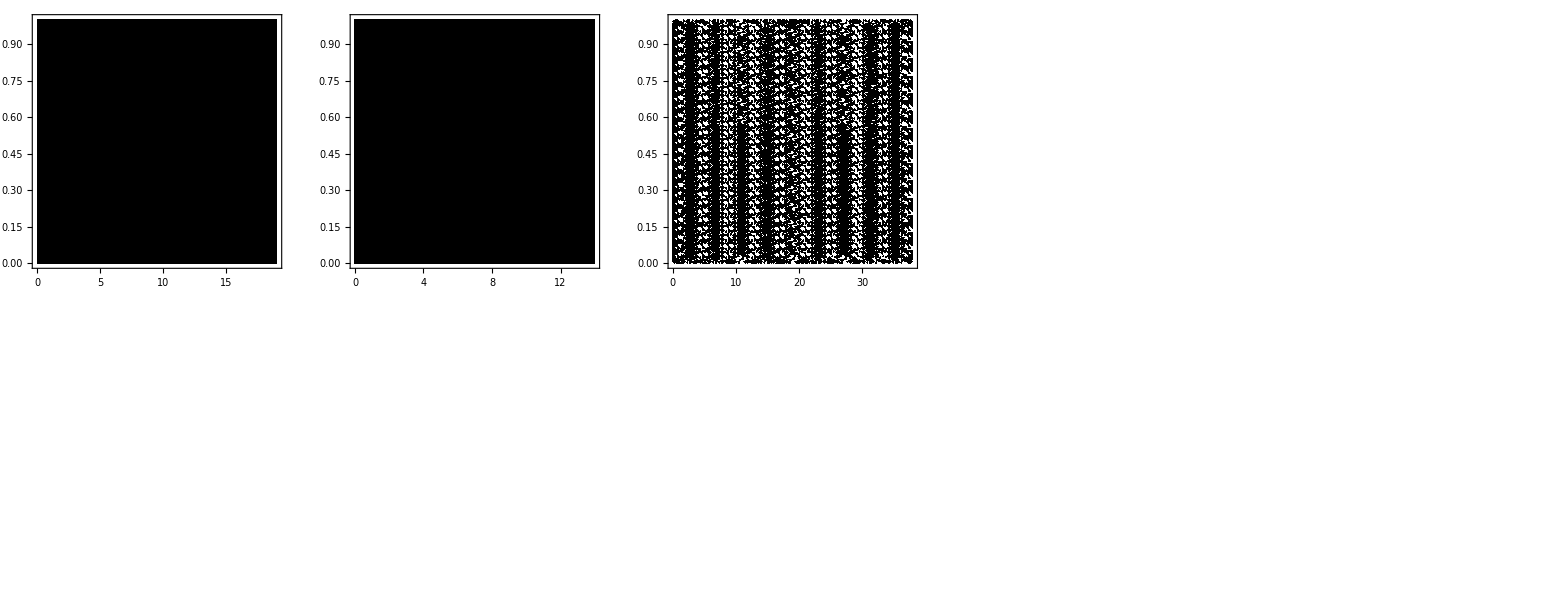

```mathematica
GraphicsGrid[Partition[Table[MakeWaves[Sqrt[Prime[k]], 10], {k, 1, 10}], 5]]
```

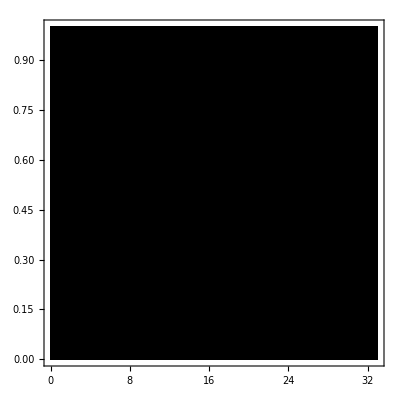

```mathematica
Table[
```

```mathematica
Table[Total[ContinuedFraction[Sqrt[7], x]], {x, 20}]
```

{2,3,4,5,9,10,11,12,16,17,18,19,23,24,25,26,30,31,32,33}

```mathematica
GetDrift[x_, n_] := Table[Total[ContinuedFraction[x, i]], {i, n}]
```

```mathematica
Max[GetDrift[3, 20]]
```

78